# Tidal Parameter Sweep, v2

## Mike Trefry July 2018

## Initialization

```mathematica
SetDirectory["C:/Users/4S/Dropbox/Tidal Mixing/"]
Get["FTLE_engine.m"]
```

C:\Users\4S\Dropbox\Tidal Mixing

## Dimensionless Parameter Groups

### Townley Number 𝒯

We define  𝒯 ≡ ω S L^2/κ_eff as the Townley number, connecting mean aquifer properties with tidal forcing frequency. Chaos promoted by low 𝒯.

### Tidal Strength 𝒢

We define  𝒢 ≡ g_p/J L as the tidal strength, connecting tidal forcing amplitude with regional gradient. Chaos promoted by high 𝒢.

### Tidal Compression Ratio 𝒞

We define  𝒞 ≡ S g_p/φ_ref as the tidal compression ratio, connecting tidal forcing amplitude with poroelasticity. Chaos promoted by  𝒞 ≲ 1.

### Flow Reversal Number ℛ

We define  ℛ ≡ σ_(ln κ)^2 𝒢 as the flow reversal number, connecting conductivity variance with tidal strength. Chaos promoted by high ℛ.

## Example Problem in WRR Manuscript

The manuscript describes properties of the solution of a problem with the following exact dimensionless parameter group values:

```mathematica
𝒯ex=10 π;
𝒢ex= 10;
𝒞ex= 0.5;
ℛex = 2 𝒢;
```

```mathematica
ExampleProblem = {Interval[{𝒯ex,𝒯ex}],Interval[{ℛex,ℛex}],"EX"};
```

## Field Studies

### Garden Island

Trefry & Bekele WRR 2004; sub-aquifer 1 is labelled “A”, sub-aquifer 2 is labelled “B”.

```mathematica
ωAO1 = 2π*0.93;
LAO1=700;
DACOlist = {170/0.005,180/0.007,170/0.007};
DAO1 = Interval[{Min[DACOlist],Max[DACOlist]}];
gpAO1 = 0.1065;
JLAO1 = Interval[{1.25,1.75}];
𝒢AO1=gpAO1/JLAO1;
σ2AO1=Interval[{0.5,2.5}];
GardenIslandAO1 = {(ωAO1*LAO1^2)/DAO1,𝒢AO1*σ2AO1,"GI"};
```

```mathematica
ωBO1 = 2π*0.93;
LBO1=700;
DBCOlist = {290/0.002,350/0.004,350/0.003};
DBO1 = Interval[{Min[DBCOlist],Max[DBCOlist]}];
gpBO1 = 0.1065;
JLBO1 = Interval[{1.25,1.75}];
𝒢BO1=gpBO1/JLBO1;
σ2BO1=Interval[{0.5,2.5}];
GardenIslandBO1 = {(ωBO1*LBO1^2)/DBO1,𝒢BO1*σ2BO1,"GI"};
```

```mathematica
ωAK1 = 2π*1.003;
LAK1=700;
DACKlist = {175/0.004,270/0.008,210/0.007};
DAK1 = Interval[{Min[DACKlist],Max[DACKlist]}];
gpAK1 = 0.1979;
JLAK1 = Interval[{1.25,1.75}];
𝒢AK1=gpAK1/JLAK1;
σ2AK1=Interval[{0.5,2.5}];
GardenIslandAK1 = {(ωAK1*LAK1^2)/DAK1,𝒢AK1*σ2AK1,"GI"};
```

```mathematica
ωBK1 = 2π*1.003;
LBK1=700;
DBCKlist = {310/0.002,440/0.001,350/0.004};
DBK1 = Interval[{Min[DBCKlist],Max[DBCKlist]}];
gpBK1 = 0.1979;
JLBK1 = Interval[{1.25,1.75}];
𝒢BK1=gpBK1/JLBK1;
σ2BK1=Interval[{0.5,2.5}];
GardenIslandBK1 = {(ωBK1*LBK1^2)/DBK1,𝒢BK1*σ2BK1,"GI"};
```

### Largs North

Trefry & Johnston GW 1998

```mathematica
ωLargs = 2π*24/13;
LLargs=Interval[{195,205}];
BLargs= Interval[{6.95,7.25}];
DLargslist = BLargs*{7.8/0.0023,9.6/0.0023,10.3/0.0021,9.6/0.0026};
DLargs = Interval[{Min[DLargslist],Max[DLargslist]}];
gpLargs = Interval[{0.5,0.8}];
JLLargs = Interval[{0.15,0.45}];
𝒢Largs=gpLargs/JLLargs;
σ2Largs=Interval[{0.5,2.5}];
LargsNorth = {(ωLargs*LLargs^2)/DLargs,𝒢Largs*σ2Largs,"LN"};
```

### Pico Azores

Cruz & Silva HJ 2001

```mathematica
ωPico = 2π*24/13;
LPico=Interval[{825,2750}];
DPicolist = {162,479};
DPico = Interval[{Min[DPicolist],Max[DPicolist]}];
gpPico= Interval[{0.21,0.6}];
JLPico = Interval[{0.1,3}];
𝒢Pico=gpPico/JLPico;
σ2Pico=Interval[{2,6}];
PicoAzores = {(ωPico*LPico^2)/(86400*DPico),𝒢Pico*σ2Pico,"P"};
```

### Dridrate

Fakir & Razack HSJ 2003

```mathematica
ωDrid = 2π*24/(12+5/12.);
LDrid=Interval[{1250.,2800}];
DDridlist = 24*Interval[{38366,906882}];
DDrid = Interval[{Min[DDridlist],Max[DDridlist]}];
gpDrid= 1.5;
JLDrid = 0.2;
𝒢Drid=gpDrid/JLDrid;
σ2Drid=Interval[{0.5,2.5}];
Dridrate= {(ωDrid*LDrid^2)/DDrid,𝒢Drid*σ2Drid,"D"};
```

### Jervoise

Smith & Hick 2001

```mathematica
ωJO1 = 2π*0.93;
LJO1=Interval[{90,180}];
DJO1list = Interval[{9100,28100}];
DJO1 = Interval[{Min[DJO1list],Max[DJO1list]}];
gpJO1= 0.1065;
JLJO1 = 0.0002*Interval[{90,180}];
𝒢JO1=gpJO1/JLJO1;
σ2JO1=Interval[{0.50,2.50}];
JervoiseO1= {(ωJO1*LJO1^2)/DJO1,𝒢JO1*σ2JO1,"J"};
```

```mathematica
ωJK1 = 2π*1.003;
LJK1=Interval[{90,180}];
DJK1list = Interval[{8400,27300}];
DJK1 = Interval[{Min[DJK1list],Max[DJK1list]}];
gpJK1= 0.1979;
JLJK1 = 0.0002*Interval[{90,180}];
𝒢JK1=gpJK1/JLJK1;
σ2JK1=Interval[{0.50,2.50}];
JervoiseK1= {(ωJK1*LJK1^2)/DJK1,𝒢JK1*σ2JK1,"J"};
```

```mathematica
JervoiseO1
JervoiseK1
```

{Interval[{1.68439,20.8049}],Interval[{1.47917,14.7917}],J}

{Interval[{1.86983,24.3078}],Interval[{2.74861,27.4861}],J}

### Swan River

Smith 1999

```mathematica
ωSRO1 = 2π*0.93;
LSRO1=Interval[{120,346}];
DSRO1list = Interval[{13500,104000}];
DSRO1 = Interval[{Min[DSRO1list],Max[DSRO1list]}];
gpSRO1= Interval[{0.04,0.07}];
JLSRO1 = 0.0002*Interval[{120,346}];
𝒢SRO1=gpSRO1/JLSRO1;
σ2SRO1=Interval[{0.50,2.50}];
SwanRiverO1= {(ωJO1*LJO1^2)/DJO1,𝒢JO1*σ2JO1,"SR"};
```

```mathematica
ωSRK1 = 2π*1.003;
LSRK1=Interval[{120,346}];
DSRK1list = Interval[{17900,113000}];
DSRK1 = Interval[{Min[DSRK1list],Max[DSRK1list]}];
gpSRK1= Interval[{0.08,0.15}];
JLSRK1 = 0.0002*Interval[{120,346}];
𝒢SRK1=gpSRK1/JLSRK1;
σ2SRK1=Interval[{0.50,2.50}];
SwanRiverK1= {(ωSRK1*LSRK1^2)/DSRK1,𝒢SRK1*σ2SRK1,"SR"};
```

### Sahel Doukkala

Fadili 2018

```mathematica
ωSDS38 = 2π*(Interval[{149.,148}]/12)/24;
LSDS38=752;
DSDS38list = 86400*Interval[{1.32,3.84}];
DSDS38 = Interval[{Min[DSDS38list],Max[DSDS38list]}];
gpSDS38= Interval[{0.92,3.45}];
JLSDS38 = Interval[{0.03,0.03}];
𝒢SDS38=gpSDS38/JLSDS38;
σ2SDS38=Interval[{0.50,2.50}];
SahelDoukkalaS38= {(ωSDS38*LSDS38^2)/DSDS38,𝒢SDS38*σ2SDS38,"SD"}
```

{Interval[{5.50351,16.1184}],Interval[{15.3333,287.5}],SD}

```mathematica
ωSDO45 = 2π*(Interval[{149.,148}]/12)/24;
LSDO45=1318;
DSDO45list = 86400*Interval[{4.13,13.02}];
DSDO45 = Interval[{Min[DSDO45list],Max[DSDO45list]}];
gpSDO45= Interval[{0.92,3.45}];
JLSDO45 = Interval[{1.04,1.84}];
𝒢SDO45=gpSDO45/JLSDO45;
σ2SDO45=Interval[{0.50,2.50}];
SahelDoukkalaO45= {(ωSDO45*LSDO45^2)/DSDO45,𝒢SDO45*σ2SDO45,"SD"}
```

{Interval[{4.98603,15.8249}],Interval[{0.25,8.29327}],SD}

## Formatted Plot

```mathematica
ClearAll[ErrorBar]
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
EB[interval_]:= interval /.{Interval[{tt1_,tt2_}],Interval[{ee1_,ee2_}],loc_} -> {{{(tt1+tt2)/2,(ee1+ee2)/2},ErrorBar[(tt2-tt1)/2,(ee2-ee1)/2]}}
EBLL[interval_]:= interval /.{Interval[{tt1_,tt2_}],Interval[{ee1_,ee2_}],loc_} -> {{{Log[10,(tt1+tt2)/2],Log[10,(ee1+ee2)/2]},ErrorBar[(Log[10,tt2]-Log[10,(tt1+tt2)/2]),(Log[10,ee2]-Log[10,(ee1+ee2)/2])]}}
EBLabel[interval_]:=interval /.{Interval[{tt1_,tt2_}],Interval[{ee1_,ee2_}],loc_} -> Text[loc,{Log[10,(tt1+tt2)/2]+0.15,Log[10,(ee1+ee2)/2]+0.1}]
```

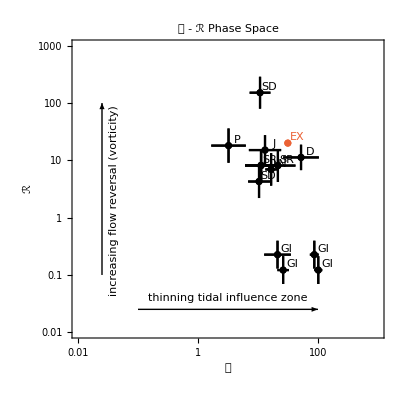

```mathematica
ErrorListPlot[{EBLL[ExampleProblem],EBLL[GardenIslandAO1],EBLL[GardenIslandBO1],EBLL[GardenIslandAK1],EBLL[GardenIslandBK1],EBLL[LargsNorth],EBLL[PicoAzores],EBLL[Dridrate],EBLL[JervoiseO1],EBLL[JervoiseK1],EBLL[SwanRiverO1],EBLL[SwanRiverK1],EBLL[SahelDoukkalaO45],EBLL[SahelDoukkalaS38]},
PlotLabel->"𝒯 - ℛ  Phase Space",
PlotStyle->{WRed,Black,Black,Black,Black,Black,Black,Black,Black,Black,Black,Black,Black,Black},
AxesOrigin->{-2,-2},
FrameTicks->{{{{Log[10,0.001],0.001,{0.02,0}},{Log[10,0.002],"",{0.01,0}},{Log[10,0.003],"",{0.01,0}},{Log[10,0.004],"",{0.01,0}},{Log[10,0.005],"",{0.01,0}},{Log[10,0.006],"",{0.01,0}},{Log[10,0.007],"",{0.01,0}},{Log[10,0.008],""},{Log[10,0.009],"",{0.01,0}},{Log[10,0.01],0.01,{0.02,0}},{Log[10,0.02],"",{0.01,0}},{Log[10,0.03],"",{0.01,0}},{Log[10,0.04],"",{0.01,0}},{Log[10,0.05],"",{0.01,0}},{Log[10,0.06],"",{0.01,0}},{Log[10,0.07],"",{0.01,0}},{Log[10,0.08],""},{Log[10,0.09],"",{0.01,0}},{Log[10,0.1],0.1,{0.02,0}},{Log[10,0.2],"",{0.01,0}},{Log[10,0.3],"",{0.01,0}},{Log[10,0.4],"",{0.01,0}},{Log[10,0.5],"",{0.01,0}},{Log[10,0.6],"",{0.01,0}},{Log[10,0.7],"",{0.012,0}},{Log[10,0.8],""},{Log[10,0.9],"",{0.01,0}},{Log[10,1],1,{0.02,0}},{Log[10,2],"",{0.01,0}},{Log[10,3],"",{0.01,0}},{Log[10,4],"",{0.01,0}},{Log[10,5],"",{0.01,0}},{Log[10,6],"",{0.01,0}},{Log[10,7],"",{0.01,0}},{Log[10,8],""},{Log[10,9],"",{0.01,0}},{Log[10,10],10,{0.02,0}},{Log[10,20],"",{0.01,0}},{Log[10,30],"",{0.01,0}},{Log[10,40],"",{0.01,0}},{Log[10,50],"",{0.01,0}},{Log[10,60],"",{0.01,0}},{Log[10,70],"",{0.01,0}},{Log[10,80],""},{Log[10,90],"",{0.01,0}},{Log[10,100],100,{0.02,0}},{Log[10,200],"",{0.01,0}},{Log[10,300],"",{0.01,0}},{Log[10,400],"",{0.01,0}},{Log[10,500],"",{0.01,0}},{Log[10,600],"",{0.01,0}},{Log[10,700],"",{0.01,0}},{Log[10,800],""},{Log[10,900],"",{0.01,0}},{Log[10,1000],1000,{0.02,0}}},{}},
{{{Log[10,0.01],0.01,{0.02,0}},{Log[10,0.02],"",{0.01,0}},{Log[10,0.03],"",{0.01,0}},{Log[10,0.04],"",{0.01,0}},{Log[10,0.05],"",{0.01,0}},{Log[10,0.06],"",{0.01,0}},{Log[10,0.07],"",{0.01,0}},{Log[10,0.08],""},{Log[10,0.09],"",{0.01,0}},{Log[10,0.1],0.1,{0.02,0}},{Log[10,0.2],"",{0.01,0}},{Log[10,0.3],"",{0.01,0}},{Log[10,0.4],"",{0.01,0}},{Log[10,0.5],"",{0.01,0}},{Log[10,0.6],"",{0.01,0}},{Log[10,0.7],"",{0.012,0}},{Log[10,0.8],""},{Log[10,0.9],"",{0.01,0}},{Log[10,1],1,{0.02,0}},{Log[10,2],"",{0.01,0}},{Log[10,3],"",{0.01,0}},{Log[10,4],"",{0.01,0}},{Log[10,5],"",{0.01,0}},{Log[10,6],"",{0.01,0}},{Log[10,7],"",{0.01,0}},{Log[10,8],""},{Log[10,9],"",{0.01,0}},{Log[10,10],10,{0.02,0}},{Log[10,20],"",{0.01,0}},{Log[10,30],"",{0.01,0}},{Log[10,40],"",{0.01,0}},{Log[10,50],"",{0.01,0}},{Log[10,60],"",{0.01,0}},{Log[10,70],"",{0.01,0}},{Log[10,80],""},{Log[10,90],"",{0.01,0}},{Log[10,100],100,{0.02,0}},{Log[10,200],"",{0.01,0}},{Log[10,300],"",{0.01,0}},{Log[10,400],"",{0.01,0}},{Log[10,500],"",{0.01,0}},{Log[10,600],"",{0.01,0}},{Log[10,700],"",{0.01,0}},{Log[10,800],""},{Log[10,900],"",{0.01,0}},{Log[10,1000],1000,{0.02,0}}},{}}},
PlotRange->{{Log[10,0.01],Log[10,1000]},{Log[10,0.01],Log[10,1000]}},Frame->True,FrameLabel->{Style["𝒯",18],Style["ℛ",18],"",""},AspectRatio->1,PlotStyle->Black,
Epilog->{Arrow[{{-1,-1.6},{2,-1.6}}],Text["thinning tidal influence zone",{0.5,-1.4}],
Arrow[{{-1.6,-1},{-1.6,2}}],Text["increasing flow reversal (vorticity)",{-1.4,0.3},{0,0},{0,1}],
EBLabel[GardenIslandAO1],EBLabel[GardenIslandAK1],EBLabel[GardenIslandBO1],EBLabel[GardenIslandBK1],
EBLabel[LargsNorth],EBLabel[PicoAzores],EBLabel[Dridrate],EBLabel[JervoiseK1],
EBLabel[JervoiseO1],EBLabel[SwanRiverK1],EBLabel[SwanRiverO1],EBLabel[SahelDoukkalaO45],EBLabel[SahelDoukkalaS38],WRed,EBLabel[ExampleProblem]}]
```

## Tidal Compressibility 𝒞 = S g_p/φ_ref

sand + limestone

```mathematica
Ss = Interval[{1.5*10^-4,3.1*10^-4}]/0.3048 (* m^-1 *)
φref = Interval[{0.2,0.5}];
gp = Interval[{0.1,10}];
𝒞 = Ss*gp/φref
```

Interval[{0.000492126,0.00101706}]

Interval[{0.0000984252,0.050853}]

sand + clay

```mathematica
Ss = Interval[{1.5*10^-4,3.1*10^-3}]/0.3048 (* m^-1 *)
φref = Interval[{0.25,0.55}];
gp = Interval[{0.1,10}];
𝒞 = Ss*gp/φref
```

Interval[{0.000492126,0.0101706}]

Interval[{0.0000894775,0.406824}]

fractured rock

```mathematica
Ss = Interval[{1*10^-6,2.1*10^-5}]/0.3048  (* m^-1 *)
φref = Interval[{0.03,0.35}];
gp = Interval[{0.1,10}];
𝒞 = Ss*gp/φref
```

Interval[{3.28084×10^-6,0.0000688976}]

Interval[{9.37383×10^-7,0.0229659}]